```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"Data"}]];
Dirs=FileNames[];
Data={};
oridata={};
Do[
grodata=Flatten[Import[FileNameJoin[{NotebookDirectory[],"Data",ToString@i<>".xlsx"}]],1];
groOD=Take[grodata,4];
gfpdata=Flatten@Take[grodata,{5,8}]/111541000;
cfpdata=Flatten@Take[grodata,{9,12}]/24578400;
mBedata=Flatten@Take[grodata,{13,16}]/7533834.19239;
dsreddata=Flatten@Take[grodata,{17,20}]/2935737.00221;
sumdata=gfpdata+cfpdata+mBedata+dsreddata;
fra0001=gfpdata/sumdata;
fra1000=cfpdata/sumdata;
fra0010=mBedata/sumdata;
fra0100=dsreddata/sumdata;
dataall=Transpose@Join[{cfpdata},{dsreddata},{mBedata},{gfpdata}];
Data=Join[Data,{dataall}];
oridata=Join[oridata,{grodata}];
,{i,1,Length@Dirs}];
Export[FileNameJoin[{NotebookDirectory[],"ccdBmixdata1.xlsx"}],oridata];
```

```mathematica
allplot={};
plotdatalist={};
plotdatamlist={};
plotdataslist={};
plotdatatotallist={};
plotdataratiomlist={};
plotdataratioslist={};
plotdataratiolist={};
Do[plotdata1=Flatten[Take[Data,All,{3i-2}]];
plotdata2=Flatten[Take[Data,All,{3i-1}]];
plotdata3=Flatten[Take[Data,All,{3i}]];
plotdata=Transpose@Join[{plotdata1},{plotdata2},{plotdata3}];
plotdatatotal=Table[Total[Transpose[Partition[plotdata,4][[i]]],{2}],{i,Length[plotdata]/4}];
plotdataratio=Flatten[Table[Transpose[Partition[plotdata,4][[i]]],{i,Length[plotdata]/4}],1];
plotdataratio1=Table[Rescale[plotdataratio[[i]],{0,Total[plotdataratio[[i]]]},{0,1}],{i,Length@plotdataratio}];
plotdataratio2=Partition[plotdataratio1,3];
plotdataratiom=Table[Mean[plotdataratio2[[i]]],{i,Length@plotdataratio2}];
plotdataratios=Table[StandardDeviation[plotdataratio2[[i]]],{i,Length@plotdataratio2}];
plotdatam=Partition[Table[Mean@plotdata[[j]],{j,Length@plotdata}],4];
plotdatas=Partition[Table[StandardDeviation@plotdata[[j]],{j,Length@plotdata}],4];
plotdatae=Partition[plotdata,4];
plotdatastack=Flatten[Table[{plotdatae[[j,1]],plotdatae[[j,1]]+plotdatae[[j,2]],plotdatae[[j,1]]+plotdatae[[j,2]]+plotdatae[[j,3]],plotdatae[[j,1]]+plotdatae[[j,2]]+plotdatae[[j,3]]+plotdatae[[j,4]]},{j,Length@plotdatae}],1];
plotdatastackm=Partition[Table[Mean@plotdatastack[[j]],{j,Length@plotdatastack}],4];
plotdatastackerr=Partition[Table[StandardDeviation@plotdatastack[[j]],{j,Length@plotdatastack}],4];

Needs["ErrorBarPlots`"];
plotdataerr1=Table[{plotdatastackm[[j,1]],plotdatastackerr[[j,1]]},{j,Length@plotdatastackm}];
plotdataerr2=Table[{plotdatastackm[[j,2]],plotdatastackerr[[j,2]]},{j,Length@plotdatastackm}];
plotdataerr3=Table[{plotdatastackm[[j,3]],plotdatastackerr[[j,3]]},{j,Length@plotdatastackm}];
plotdataerr4=Table[{plotdatastackm[[j,4]],plotdatastackerr[[j,4]]},{j,Length@plotdatastackm}];
errorplot1=ErrorListPlot[plotdataerr1,PlotRange->{{1,25},{0,1.2}},PlotStyle->{RGBColor[200/255,200/255,169/255]}];
errorplot2=ErrorListPlot[plotdataerr2,PlotRange->{{1,25},{0,1.2}},PlotStyle->{RGBColor[254/255,67/255,101/255]}];
errorplot3=ErrorListPlot[plotdataerr3,PlotRange->{{1,25},{0,1.2}},PlotStyle->{RGBColor[252/255,157/255,154/255]}];
errorplot4=ErrorListPlot[plotdataerr4,PlotRange->{{1,25},{0,1.2}},PlotStyle->{RGBColor[131/255,175/255,155/255]}];


plot=StackedListPlot[Transpose@plotdatam,PlotStyle->{RGBColor[200/255,200/255,169/255],RGBColor[254/255,67/255,101/255],RGBColor[252/255,157/255,154/255],RGBColor[131/255,175/255,155/255]},Frame->True,FrameTicks->{{{0,0.3,0.6,0.9,1.2},None},{{1,5,9,10,13,16,17,20,23},None}},FrameStyle->Directive[Black,20],PlotMarkers->Automatic,PlotRange->{{0,25},{0,1.2}},ImageSize->Large];
combplot=Show[plot,errorplot1,errorplot2,errorplot3,errorplot4];
allplot=Join[allplot,{combplot}];
plotdatalist=Join[plotdatalist,{plotdata}];
plotdatamlist=Join[plotdatamlist,{plotdatam}];
plotdataslist=Join[plotdataslist,{plotdatas}];
plotdatatotallist=Join[plotdatatotallist,{plotdatatotal}];
plotdataratiomlist=Join[plotdataratiomlist,{plotdataratiom}];
plotdataratioslist=Join[plotdataratioslist,{plotdataratios}];
plotdataratiolist=Join[plotdataratiolist,{plotdataratio2}];
,{i,1,16}];
allplot=Partition[allplot,4];
gridplot=Grid[allplot];
Export[FileNameJoin[{NotebookDirectory[],"plot","Gridplot2.tif"}],gridplot];
Export[FileNameJoin[{NotebookDirectory[],"growthdata.xlsx"}],plotdatamlist];
Export[FileNameJoin[{NotebookDirectory[],"growthdataD.xlsx"}],plotdataslist];
Export[FileNameJoin[{NotebookDirectory[],"growthratio.xlsx"}],plotdataratiolist];
```

```mathematica
stru=Flatten[Take[plotdatamlist,All,{-1}],1];
BarChart[stru,ChartLayout->"Stacked",ChartStyle->{RGBColor[200/255,200/255,169/255],RGBColor[254/255,67/255,101/255],RGBColor[252/255,157/255,154/255],RGBColor[131/255,175/255,155/255]}];
G1end=Flatten[Take[plotdatatotallist,All,{9}],1];
G2end=Flatten[Take[plotdatatotallist,All,{16}],1];
G3end=Flatten[Take[plotdatatotallist,All,{24}],1];
ratio1=Transpose@Join[{Flatten@Take[Flatten[Take[plotdataratiomlist,All,{9}],1],All,{4}]},{Flatten@Take[Flatten[Take[plotdataratioslist,All,{9}],1],All,{4}]}];
ratio2=Transpose@Join[{Flatten@Take[Flatten[Take[plotdataratiomlist,All,{16}],1],All,{4}]},{Flatten@Take[Flatten[Take[plotdataratioslist,All,{16}],1],All,{4}]}];
ratio3=Transpose@Join[{Flatten@Take[Flatten[Take[plotdataratiomlist,All,{24}],1],All,{4}]}
,{Flatten@Take[Flatten[Take[plotdataratioslist,All,{24}],1],All,{4}]}];
Export[FileNameJoin[{NotebookDirectory[],"ccdBanalysis.xlsx"}],"Sheets"->{"end1"->G1end,"end2"->G2end,"end3"->G3end,"ratio1"->ratio1,"ratio2"->ratio2,"ratio3"->ratio3},"Rules"];
```

```mathematica
inistru=Flatten[Take[plotdatamlist,All,{1}],1];
Do[iniplot=PieChart3D[inistru[[i]],ChartStyle->{RGBColor[200/255,200/255,169/255],RGBColor[254/255,67/255,101/255],RGBColor[252/255,157/255,154/255],RGBColor[131/255,175/255,155/255]}];
Export[FileNameJoin[{NotebookDirectory[],"plot","piechart-"<>ToString@i<>".tif"}],iniplot];
,{i,Length@inistru}];
```

```mathematica
finalstru=Flatten[Take[plotdatamlist,All,{-1}],1];
Do[finalplot=PieChart3D[finalstru[[i]],ChartStyle->{RGBColor[200/255,200/255,169/255],RGBColor[254/255,67/255,101/255],RGBColor[252/255,157/255,154/255],RGBColor[131/255,175/255,155/255]}];
Export[FileNameJoin[{NotebookDirectory[],"plot","fchart-"<>ToString@i<>".tif"}],finalplot];
,{i,Length@finalstru}];
```

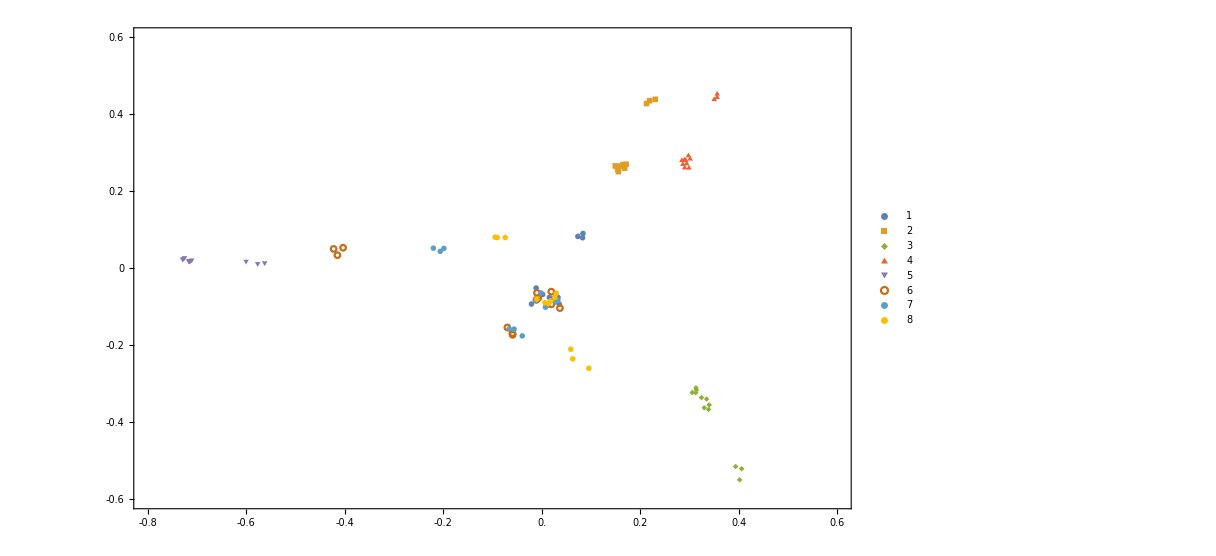

```mathematica
pcadata={};
Do[inidata=plotdataratiolist[[i]][[1]];
m1data=plotdataratiolist[[i]][[9]];
m2data=plotdataratiolist[[i]][[16]];
finaldata=plotdataratiolist[[i]][[24]];
pcadata=Join[pcadata,{inidata},{m1data},{m2data},{finaldata}];
,{i,9,16}];
pca=Partition[Take[PrincipalComponents[Flatten[pcadata,1]],All,{1,2}],12];
pcaplot=ListPlot[pca,PlotStyle->PointSize[Large],AxesStyle->Directive[Thickness[0.005],Opacity[0.56],Dashed],PlotLegends->Automatic,PlotRange->{{-0.8,0.6},{-0.6,0.6}},Frame->True,FrameStyle->Directive[Thickness[0.006],Black,Bold,40],FrameTicks->{{{#,#,{0.01,0}}&/@{-0.6,-0.4,-0.2,0,0.2,0.4,0.6},None},{{#,#,{0.01,0}}&/@Range[-0.8,0.6,0.2],None}},PlotMarkers->{Automatic,Scaled[0.03]},PlotRange->{{0,25},{0,0.4}},ImageSize->900]
Export[FileNameJoin[{NotebookDirectory[],"plot","ccdBfractionpca.tif"}],pcaplot];
```